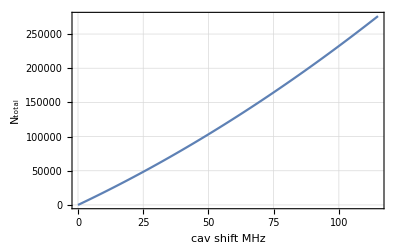

316033.

```mathematica
Nt[cavShiftMHz_] := (cavShiftMHz^2+cavShiftMHz*350)/(0.440^2);
Plot[Nt[cavShiftMHz], {cavShiftMHz, 0, 115}, PlotRangePadding->None, Frame->True, GridLines->Automatic, FrameLabel->{"cav shift MHz", "N_total"}]
 (cavShiftMHz^2+cavShiftMHz*350)/(0.440^2)/. cavShiftMHz->3.2*40
```

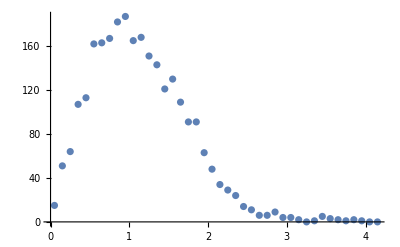

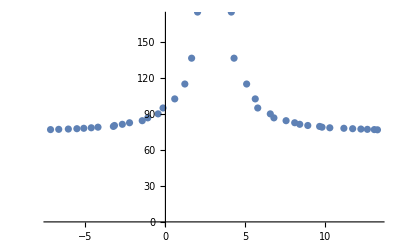

doubleDataset.tsv

doubleDataset.csv

```mathematica
data = RandomVariate[NormalDistribution[9, 5], 10^4];
data={{0.05,15},{0.15,51},{0.25,64},{0.35,107},{0.45,113},{0.55,162},{0.65,163},{0.75,167},{0.85,182},{0.95,187},{1.05,165},{1.15,168},{1.25,151},{1.35,143},{1.45,121},{1.55,130},{1.65,109},{1.75,91},{1.85,91},{1.95,63},{2.05,48},{2.15,34},{2.25,29},{2.35,24},{2.45,14},{2.55,11},{2.65,6},{2.75,6},{2.85,9},{2.95,4},{3.05,4},{3.15,2},{3.25,0},{3.35,1},{3.45,5},{3.55,3},{3.65,2},{3.75,1},{3.85,2},{3.95,1},{4.05,0},{4.15,0}};
data2 = Table[{ii+(RandomReal[]-.5)/2, 200 1/(1+(ii-3)^2)+75}, {ii, -7, 13.5, 21./42}];


data3 = Table[{data[[ii, 1]], data[[ii, 2]], data2[[ii, 1]], data2[[ii, 2]]}, {ii, 1, 42}];
ListPlot[data3[[;;, 1;;2]]]
ListPlot[data3[[;;, 3;;4]]]
SetDirectory[NotebookDirectory[]];
data3 = Insert[data3, {"Gaussian x-vals", "Gaussian y-vals", "Lorentzian x-vals", "Lorentzian y-vals"}, 1];
Export["doubleDataset.tsv", data3, "TSV"]
Export["doubleDataset.csv",data3, "CSV"]
```